```mathematica
SetDirectory["/home/jadeleon/Documents/component-erasing-maps"];
Import["mathematica/quantumJA.m"];
CurrentValue[EvaluationNotebook[],DefaultNaturalLanguage]="Spanish";
TwoQubits=ToExpression[Import["results/TwoQubits.txt","List"]];
OneQubit=ToExpression[Import["results/OneQubit.txt","List"]];
```

```mathematica
OneQubit
```

{qubit results #1,{1,0,0,0},{1,1,0,0},{1,0,1,0},{1,0,0,1},{1,1,1,1}}

## Minors:

El criterio de Sylvester, que es con los leading principal minors (que sí son n en una matriz de n×n), es para positividad definida. Para positividad semidefinida ahuevo hay que evaluar que todos los principal minors sean positivos, y el número de principal minors para una matriz de 16×16 son:

```mathematica
Binomial[16,#]&/@Range[16]//Total
```

65535

osea 2^n-1 con n el número de qubits en nuestro caso.

#### Comparar eigenvalores:

```mathematica
eigvTwoQ=(QC[#,2]//Reshuffle//Eigenvalues)&/@TwoQubits;
```

#### Siguiente: comparar los eigenv

```mathematica
eigvTwoQ=1/4eigvTwoQ;
```

## Eigenvalores de la matriz de Choi:

## 1 qubit

```mathematica
OneQubit={{1,0,0,0},{1,1,0,0},{1,0,1,0},{1,0,0,1},{1,1,1,1}};
Export["/home/jadeleon/Documents/component-erasing-maps/results/OneQubit.txt",OneQubit];
```

#### Eigenvalores (ordenados):

```mathematica
1/2(QC[#,1]//Reshuffle//Eigenvalues)&/@OneQubit
```

{{1/4,1/4,1/4,1/4},{1/2,1/2,0,0},{1/2,1/2,0,0},{1/2,1/2,0,0},{1,0,0,0}}

#### 1 componente invariante

```mathematica
eigvTwoQ[[1]]
```

{1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16}

#### 2 componentes invariantes

```mathematica
eigvTwoQ[[2;;16]]
```

{{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,0,0,0,0,0,0,0,0},{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,0,0,0,0,0,0,0,0},{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,0,0,0,0,0,0,0,0},{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,0,0,0,0,0,0,0,0},{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,0,0,0,0,0,0,0,0},{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,0,0,0,0,0,0,0,0},{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,0,0,0,0,0,0,0,0},{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,0,0,0,0,0,0,0,0},{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,0,0,0,0,0,0,0,0},{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,0,0,0,0,0,0,0,0},{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,0,0,0,0,0,0,0,0},{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,0,0,0,0,0,0,0,0},{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,0,0,0,0,0,0,0,0},{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,0,0,0,0,0,0,0,0},{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,0,0,0,0,0,0,0,0}}

#### 4 componentes invariantes

```mathematica
(QC[TwoQubits[[#]],2]//Reshuffle//Eigenvectors//MatrixPlot)&/@Range[2,16]
```

```mathematica
eigvTwoQ[[17;;51]]
```

{{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0},{1/4,1/4,1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0}}

#### ¿y si revisamos los eigv de una operación que también deja 4 componentes invariantes pero no es CP?

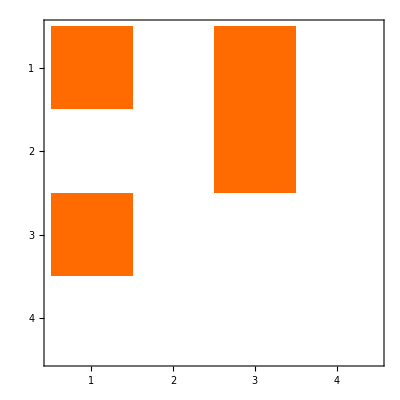

{1/4,1/4,-1/8,-1/8,1/8,1/8,1/8,1/8,1/8,1/8,0,0,0,0,0,0}

```mathematica
SparseArray[{{1,1},{1,3},{3,1},{2,3}}->{1,1,1,1},{4,4}]//Normal//MatrixPlot
1/4QC[SparseArray[{{1,1},{1,3},{3,1},{2,3}}->{1,1,1,1},{4,4}]//Normal//Flatten,2]//Reshuffle//Eigenvalues
```

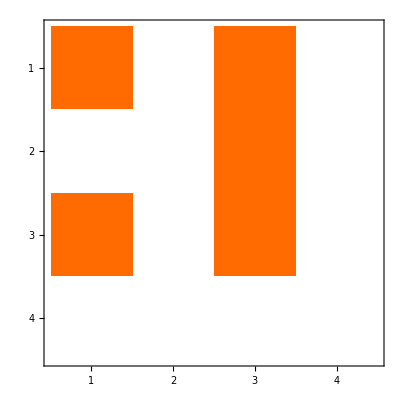

{5/16,5/16,3/16,3/16,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,1/16,1/16,1/16,1/16,1/16,1/16}

```mathematica
SparseArray[{{1,1},{1,3},{3,1},{2,3},{3,3}}->{1,1,1,1,1},{4,4}]//Normal//MatrixPlot
QC[SparseArray[{{1,1},{1,3},{3,1},{2,3},{3,3}}->{1,1,1,1,1},{4,4}]//Normal//Flatten,2]//Reshuffle//Eigenvalues
```

#### ¿y los de alguna operación que deje algún número diferente de 2^k componentes invariantes?

#### 8 componentes invariantes

```mathematica
eigvTwoQ[[52;;66]]
```

{{1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

#### 16 componentes invariantes

```mathematica
eigvTwoQ[[67]]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}